200

Так было в самом начале

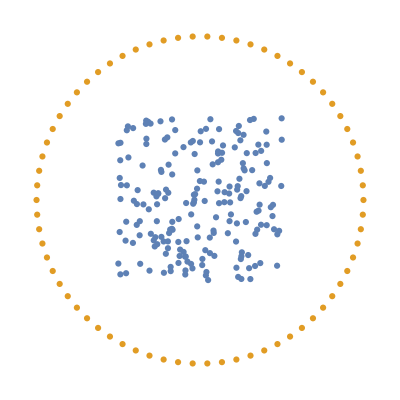

Import::nffil: File not found during Import.

244

Так вышло

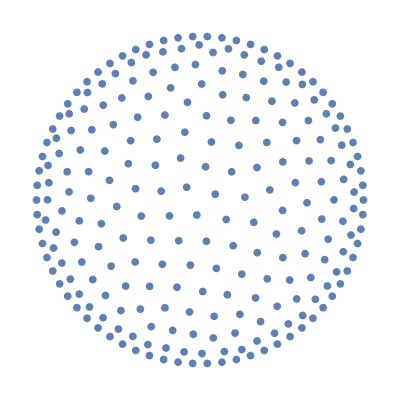

Part::partd: Part specification $Failed ⟦ 1, 1 ⟧ is longer than depth of object.

Триангуляция

Show::shx: No graphical objects to show.

Show[{}]

Cамый маленький угол в триангуляции

∞

Cамый большой угол в триангуляции

-∞

Самая большая сторона в триангуляции

-∞

Самая маленькая сторона в триангуляции

∞

Отношение сторон

Infinity::indet: Indeterminate expression 0\ (-∞) encountered.

Indeterminate

Отношение сторон для треугольников

-∞

∞

```mathematica
SetDirectory[NotebookDirectory[]];
Wall= Import["Init_wallr.dat"];
Length[Nodes]
Nodes = Import ["Init_insider.dat"];
Print["Так было в самом начале"]
ListPlot[{Nodes,Wall}, AspectRatio->1,Axes->False]

Inside= Import["triangles.dat"];


Allal = Import["allr.dat"];
Length[Allal]
Print["Так вышло"]
ListPlot[Allal,AspectRatio->1,Axes->False]
Ntri= Inside[[1,1]];
For[i = 1, i≤ Ntri, i+=3, Elems[i] ={};
AppendTo[Elems[i],Inside[[i+1]]]; AppendTo[Elems[i],Inside[[i+2]]]; AppendTo[Elems[i],Inside[[i+3]]];];
tr = {}; sf = {};
For [i = 1, i≤Ntri ,i+=3, AppendTo[tr,Graphics[{EdgeForm[Blue],RGBColor[i 5/(10*Ntri),(Ntri-i) 10/(10*Ntri),(Ntri*-i) 3/(10*Ntri)],Opacity[i/Ntri],Triangle[Elems[i]]}]]];


MaxAngles = {};
MinAngles = {};
Len ={};
MaxLen = {};
MinLen = {}; 
For [i = 4, i≤Ntri ,i+=3,
u = {Elems[i][[2,1]]-Elems[i][[1,1]], Elems[i][[2,2]] -Elems[i][[1,2]]};nu = Norm[u];
v = {Elems[i][[3,1]]-Elems[i][[1,1]], Elems[i][[3,2]] -Elems[i][[1,2]]};nv = Norm[v];
w = {Elems[i][[2,1]]-Elems[i][[3,1]], Elems[i][[2,2]] -Elems[i][[3,2]]};nw = Norm[w];
If[nv<nw+nu,
AppendTo[MaxAngles, Max[{Re[180*VectorAngle[-u,-w]/Pi] ,Re[180* VectorAngle[u,v]/Pi],Re[180*VectorAngle[-v,w]/Pi]}]];
AppendTo[MinAngles, Min[{180*VectorAngle[-u,-w]/Pi ,180* VectorAngle[u,v]/Pi,180*VectorAngle[-v,w]/Pi}]];
AppendTo[sf,Graphics[Circumsphere[Elems[i]]]];
AppendTo[MaxLen, Max[nu,nv,nw]];
AppendTo[MinLen, Min[nu,nv,nw]];
AppendTo[Len, Max[nu,nv,nw]/Min[nu,nv,nw]];]

]

Print["Триангуляция"]
g =Graphics[{White,Disk[{1,1},0.5]}];
Show[tr]
Print["Cамый маленький угол в триангуляции"]
Min[MinAngles]
Print["Cамый большой угол в триангуляции"]
Max[MaxAngles]
Print["Самая большая сторона в триангуляции"]
Max[MaxLen]
Print["Самая маленькая сторона в триангуляции"]
Min[MinLen]

Print["Отношение сторон"]
Max[MaxLen]/Min[MinLen]
Print["Отношение сторон для треугольников"]
Max[Len]
Min[Len]
```

```mathematica
ListLinePlot[Len]
```

-Graphics-

```mathematica
Mean[Len]
```

Mean[{}]

```mathematica
Data  = {{1,2,3},{2,3,4},{3,4,5}};
```

```mathematica
ListPointPlot3D[Data,PlotRange->{{0,1},{0,1},{0,1}}]
```

-Graphics3D-

```mathematica
ListPlot[Allal,AspectRatio->1,Axes->False]
```

-Graphics-